```mathematica
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2meV=1000*8.617332478*10^−5;K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)

(*define sigma and8 kappa kernels*)
(*temp in energy units*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
```

```mathematica
temps2={0,300,760,1900,2500,3200,3800}
K2eV*temps2
```

{0,300,760,1900,2500,3200,3800}

{0.,0.025852,0.0654917,0.163729,0.215433,0.275755,0.327459}

## Simple initial DOS example

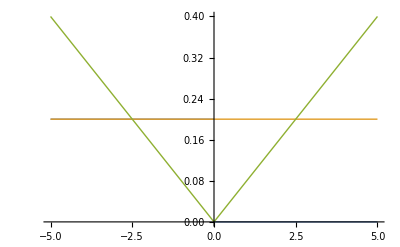

```mathematica
(*insulator and metal DOS*)
B=5;
IMDOS={HeavisideTheta[-energy]/(NIntegrate[HeavisideTheta[-energy],{energy,-B,0}]),0.5/(NIntegrate[0.5,{energy,-B,0}]),Sqrt[energy^2]/(NIntegrate[Sqrt[energy^2],{energy,-B,0}])};
Plot[IMDOS,{energy,-B,B},PlotStyle->Thick]
```

```mathematica
plotoptionsigma={"Sigma kernel times Insulator","Sigma kernel times Metal"};
plotoptionkappa={"Kappa kernel times Insulator","Kappa kernel times Metal"};
```

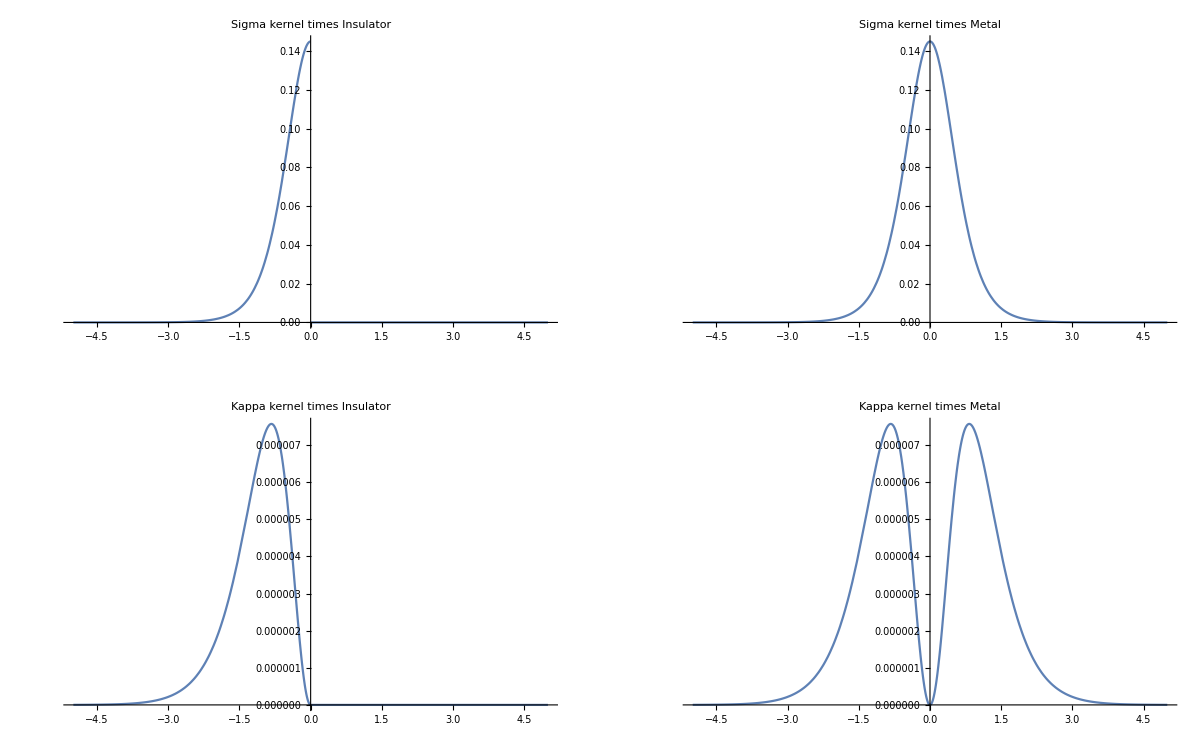

```mathematica
GraphicsGrid[{Table[Plot[{Evaluate[IMDOS[[i]]*sigmaK[energy,4000]]},{energy,-B,B},PlotRange->All,PlotLabel->Evaluate[plotoptionsigma[[i]]]],{i,1,2}],Table[Plot[{Evaluate[IMDOS[[i]]*kappaK[energy,4000]]},{energy,-B,B},PlotRange->All,PlotLabel->Evaluate[plotoptionkappa[[i]]]],{i,1,2
}]},ImageSize->1200]
```

```mathematica
sigmaT=Table[Table[{T,NIntegrate[{Evaluate[IMDOS[[i]]*sigmaK[energy,T]]},{energy,-B,B}]},{i,1,3}],{T,100,4000,100}];
kappaT=Table[Table[{T,NIntegrate[{Evaluate[IMDOS[[i]]*kappaK[energy,T]]},{energy,-B,B}]},{i,1,3}],{T,100,4000,100}];
temmps=Table[T,{T,100,4000,100}]
```

{100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900,4000}

```mathematica
plotoptionsigma2={"Sigma - Insulator DOS","Sigma - Metal DOS","Sigma - MOD DOS"};
plotoptionkappa2={"Kappa - Insulator DOS","Kappa - metal DOS","Kappa- MOD DOS"};
plotoptionsigmakappa={"Kappa/Sigma - Insulator DOS","Kappa/Sigma - Metal DOS","Kappa/sigma - MOD DOS"};
plotoptionlorenz={"Lorenz - Insulator DOS","Lorenz - Metal DOS","Lorenz - MOD DOS"};
```

```mathematica
GraphicsGrid[{Table[ListPlot[Transpose[Transpose[sigmaT][[i]]],PlotLabel->Evaluate[plotoptionsigma2[[i]]],PlotLegends->SwatchLegend[{"symmetric","large val","large cond"}]],{i,1,3}]},ImageSize->900]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListLinePlot[Transpose[Transpose[kappaT][[i]]],PlotLabel->Evaluate[plotoptionkappa2[[i]]],PlotLegends->SwatchLegend[{"symmetric","large val","large cond"}]],{i,1,3}]},ImageSize->600]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListPlot[Transpose[Transpose[kappaT/sigmaT][[i]]],PlotLabel->Evaluate[plotoptionsigmakappa[[i]]],PlotLegends->SwatchLegend[{"symmetric","large val","large cond"}]],{i,1,3}]},ImageSize->900]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListPlot[Transpose[Transpose[kappaT/(sigmaT)][[i]]*temmps^-1],PlotLabel->Evaluate[plotoptionlorenz[[i]]],PlotLegends->SwatchLegend[{"symmetric","large val","large cond"}],ImageSize->400],{i,1,3}]},ImageSize->1500]
```

-Graphics-

## More complicated example

ClearAll

{0.024 (0.5+Abs[energy]^2),0.134164 (0.5+√Abs[energy]),0.08 (0.5+Abs[energy]),0.0344828 (0.5+Abs[7.97885 ⅇ^(-12.5 (-1+energy)^2)-7.97885 ⅇ^(-12.5 (1+energy)^2)+2 energy])}

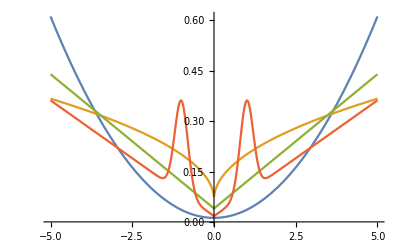

```mathematica
UPshift=0.5;
ClearAll
symDOS={(Abs[energy^2]+UPshift)/NIntegrate[Abs[energy^(2)],{energy,-B,0}],(Abs[energy^(1/2)]+UPshift)/NIntegrate[Abs[energy^(1/2)],{energy,-B,0}],(Abs[energy]+UPshift)/NIntegrate[Abs[energy],{energy,-B,0}],(Abs[2energy-4PDF[NormalDistribution[-1,0.2],energy]+4PDF[NormalDistribution[1,0.2],energy]]+UPshift)/(Integrate[Abs[2energy-4PDF[NormalDistribution[-1,0.2],energy]+4PDF[NormalDistribution[1,0.2],energy]],{energy,-B,0}])}
Plot[Evaluate@symDOS,{energy,-B,B}]
```

```mathematica
sigmaTcomp=Table[Table[{T,NIntegrate[Evaluate[symDOS[[i]]*sigmaK[energy,T]],{energy,-4B,4B}]},{i,1,4}],{T,100,4000,100}];
kappaTcomp=Table[Table[{T,NIntegrate[Evaluate[symDOS[[i]]*kappaK[energy,T]],{energy,-4B,4B}]},{i,1,4}],{T,100,4000,100}];
```

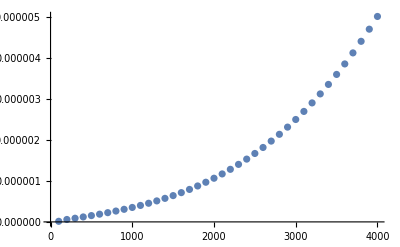

```mathematica
ListPlot@Transpose[kappaTcomp][[1]]
```

{AspectRatio→1,Filling→Bottom,FillingStyle→Directive[Opacity[0.1],RGBColor[0, 0, 1]],FrameLabel→{Energy-E_F,Density of states},PlotStyle→Thickness[0.01],FrameTicks→None,Frame→True,ImageSize→200}

{AspectRatio→1,FillingStyle→Directive[Opacity[0.1],GrayLevel[0.5]],Filling→Bottom,FrameLabel→{T,κ},PlotStyle→Thickness[0.01],FrameTicks→None,Frame→True,ImageSize→200}

{AspectRatio→1,FillingStyle→Directive[Opacity[0.1],RGBColor[1, 0.5, 0]],Filling→Bottom,FrameLabel→{T,σ},PlotStyle→Thickness[0.01],FrameTicks→None,Frame→True,ImageSize→200}

{PlotRange→{{0,4000},{1/50000000,7.5×10^-8}},AspectRatio→1,Filling→Bottom,FillingStyle→Directive[Opacity[0.1],RGBColor[1, 0, 0]],FrameLabel→{T,Lorenz number},PlotStyle→Thickness[0.01],FrameTicks→None,Frame→True,ImageSize→200}

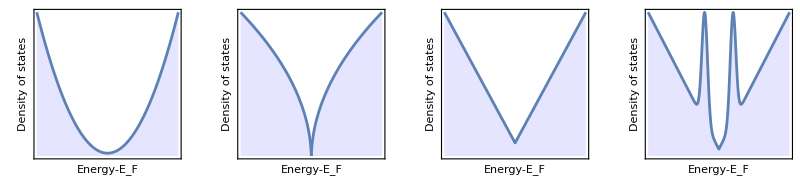

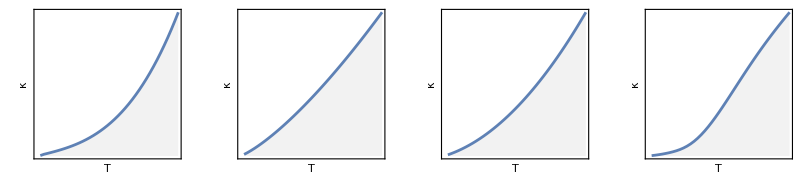

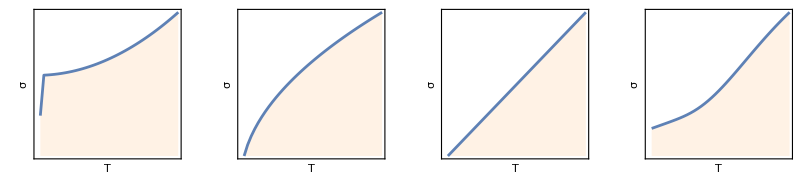

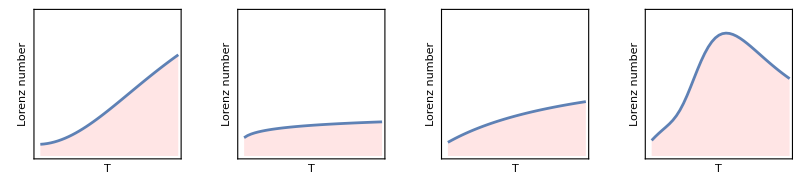

```mathematica
optionsDOS={AspectRatio->1,Filling->Bottom,FillingStyle->Directive[Opacity[0.1],Blue],FrameLabel->{Style["Energy-E_F",15],Style["Density of states",15]},PlotStyle->Thickness[0.01],FrameTicks->None,Frame->True,ImageSize->200}
optionsKappa={AspectRatio->1,FillingStyle->Directive[Opacity[0.1],Gray],Filling->Bottom,FrameLabel->{Style["T",15],Style["κ",15]},PlotStyle->Thickness[0.01],FrameTicks->None,Frame->True,ImageSize->200}
optionsSigma={AspectRatio->1,FillingStyle->Directive[Opacity[0.1],Orange],Filling->Bottom,FrameLabel->{Style["T",15],Style["σ",15]},PlotStyle->Thickness[0.01],FrameTicks->None,Frame->True,ImageSize->200}
optionsLorenz={PlotRange->{{0,4000},{2*10^-8,7.5*10^-8}},AspectRatio->1,Filling->Bottom,FillingStyle->Directive[Opacity[0.1],Red],FrameLabel->{Style["T",15],Style["Lorenz number",15]},PlotStyle->Thickness[0.01],FrameTicks->None,Frame->True,ImageSize->200}
GraphicsGrid[{Table[Plot[Evaluate[symDOS[[i]]],{energy,-B,B},Evaluate@optionsDOS],{i,1,4}]},ImageSize->800]
GraphicsGrid[{Table[ListLinePlot[Transpose[kappaTcomp][[i]],Evaluate@optionsKappa],{i,1,4}]},ImageSize->800]
GraphicsGrid[{Table[ListLinePlot[Transpose[sigmaTcomp][[i]],Evaluate@optionsSigma],{i,1,4}]},ImageSize->800]
lorenzTcomp=Table[Transpose@{temmps,Transpose[Transpose[kappaTcomp][[i]]][[2]]/(Transpose[Transpose[sigmaTcomp][[i]]][[2]]*temmps)},{i,1,4}];
GraphicsGrid[{Table[ListLinePlot[lorenzTcomp[[i]],Evaluate@optionsLorenz],{i,1,4}]},ImageSize->800]
```

```mathematica
symDOS
```

{0.024 (0.5+Abs[energy]^2),0.134164 (0.5+√Abs[energy]),0.08 (0.5+Abs[energy]),0.0344828 (0.5+Abs[7.97885 ⅇ^(-12.5 (-1+energy)^2)-7.97885 ⅇ^(-12.5 (1+energy)^2)+2 energy])}

```mathematica
(*Plot[Evaluate[symDOS[[1]],{energy,-B,B}]
GraphicsGrid[{Table[Plot[symDOS[[i]],{energy,-B,B}],{i,1,4}]},ImageSize->900]*)
```

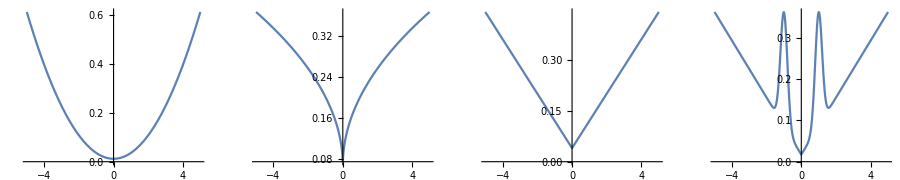

```mathematica
GraphicsGrid[{Table[Plot[Evaluate[symDOS[[i]]],{energy,-B,B}],{i,1,4}]},ImageSize->900]
```

-Graphics-

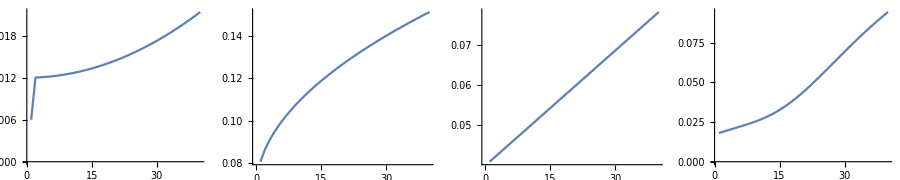

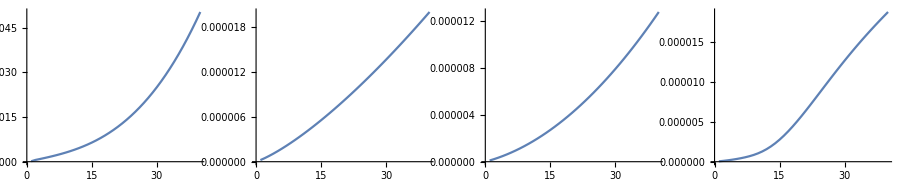

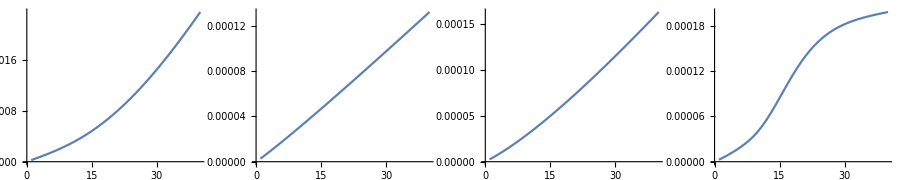

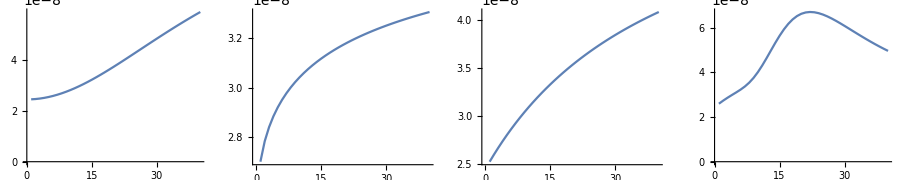

```mathematica
plotoptionlorenzComp={"Lorenz - Abs[energy^(1/2) DOS","Lorenz - Abs[energy] DOS","Lorenz - Abs[energy^2] DOS","Lorenz - Abs[energy]+Gauss DOS"};

GraphicsGrid[{Table[Plot[Evaluate[symDOS[[i]]],{energy,-B,B}],{i,1,4}]},ImageSize->900]
GraphicsGrid[{Table[ListLinePlot[Transpose[Transpose[sigmaTcomp][[i]]]],{i,1,4}]},ImageSize->900]
GraphicsGrid[{Table[ListLinePlot[Transpose[Transpose[kappaTcomp][[i]]]],{i,1,4}]},ImageSize->900]
GraphicsGrid[{Table[ListLinePlot[Transpose[Transpose[kappaTcomp/sigmaTcomp][[i]]]],{i,1,4}]},ImageSize->900]
GraphicsGrid[{Table[ListLinePlot[Transpose[Transpose[kappaTcomp/(sigmaTcomp*temmps)][[i]]]],{i,1,4}]},ImageSize->900]
```

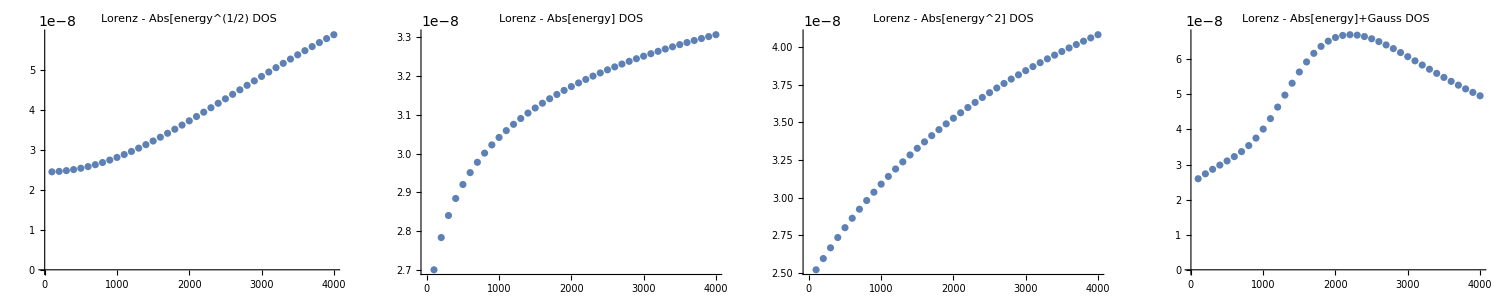

```mathematica
GraphicsGrid[{Table[ListPlot[Transpose[{temmps,Transpose[Transpose[kappaTcomp/(sigmaTcomp)][[i]]*temmps^-1][[1]]}],PlotLabel->Evaluate[plotoptionlorenzComp[[i]]],ImageSize->400],{i,1,4}]},ImageSize->1500]
```

Algebraic solution to Lorenz number

(Integrate[kappaK[energy,T],energy])/Integrate[sigmaK[energy,T],energy]//Simplify

-1/T11604.5 (1.+ⅇ^((11604.5 energy)/T)) (energy ((0.0000861733-0.0000861733/(1.+ⅇ^((11604.5 energy)/T))) energy-1.48517×10^-8 T Log[1.+ⅇ^((11604.5 energy)/T)])-1.27982×10^-12 T^2 PolyLog[2.,-1. ⅇ^((11604.5 energy)/T)])

Evaluate[(Integrate[kappaK[energy,T],energy])/Integrate[sigmaK[energy,T],energy]]

-1/T11604.5 (1.+2.71828^((11604.5 energy)/T)) (energy ((0.0000861733-0.0000861733/(1.+ⅇ^((11604.5 energy)/T))) energy-1.48517×10^-8 T Log[1.+ⅇ^((11604.5 energy)/T)])-1.27982×10^-12 T^2 PolyLog[2.,-1. ⅇ^((11604.5 energy)/T)])

Evaluate[(Integrate[kappaK[energy,T],energy])/Integrate[sigmaK[energy,T],energy]]/.T→100

-116.045 (1.+2.71828^(116.045 energy)) (energy ((0.0000861733-0.0000861733/(1.+ⅇ^(116.045 energy))) energy-1.48517×10^-6 Log[1.+ⅇ^(116.045 energy)])-1.27982×10^-8 PolyLog[2.,-1. ⅇ^(116.045 energy)])

Evaluate[(Integrate[IMDOS*kappaK[energy,T],{energy,-T,T}])/(T*IMDOS*Integrate[sigmaK[energy,T],{energy,-T,T}])]

{ConditionalExpression[1/HeavisideTheta[-Global`energy]11604.5 (HeavisideTheta[-2 Global`T] HeavisideTheta[-Global`T] (1.05261×10^-12+1.05261×10^-12 HeavisideTheta[Global`T])+(-0.0000861733-0.0000861733 HeavisideTheta[-Global`T]) HeavisideTheta[Global`T] HeavisideTheta[2 Global`T]),Global`T∈Reals],2.443×10^-8,ConditionalExpression[-(4. Global`T)/(√((Global`energy)^2)),Re[Global`T]>0&&Im[Global`T]==0]}

## Isotropic scattering matrix but real DOS example

```mathematica
(*PERFECT : #DOS(states/Ry/spin)-0.98056222E+00 0.77605174E+00 0.10000000E-03 0.0000 0000E+00 17567*)
(*FRENKEL : DOS(states/Ry/spin)-0.94420567E+00 0.48408628E+00 0.10000000E-03 0.000 00000E+00 14283*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Lorenz/46583_lorenz"];
filesL={"perfDOS" ,"frenDOS"};
filesL2={"46583_kp19_50hte_SP_perfect.transdos" ,"46583_kp19_50hte_SP_frenkel.transdos"};
lorenz=Table[ReadList[filesL[[i]],{Word,Word,Word}],{i,1,2}];
```

```mathematica
eV2ryd=1/13.605698066;ryd2eV=13.605698066;
perfDOS=Transpose@{Table[ryd2eV*Internal`StringToDouble[lorenz[[1]][[i]][[1]]],{i,1,lorenz[[1]]//Length}],Table[eV2ryd*Internal`StringToDouble[lorenz[[1]][[i]][[2]]],{i,1,lorenz[[1]]//Length}]};
frenDOS=Transpose@{Table[ryd2eV*Internal`StringToDouble[lorenz[[2]][[i]][[1]]],{i,1,lorenz[[2]]//Length}],Table[eV2ryd*Internal`StringToDouble[lorenz[[2]][[i]][[2]]],{i,1,lorenz[[2]]//Length}]};
```

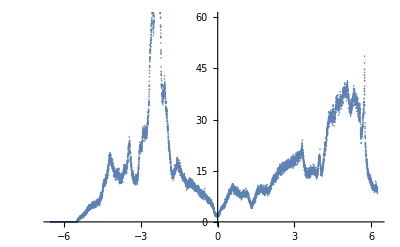

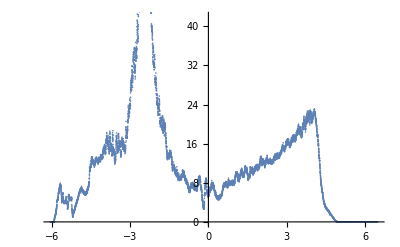

```mathematica
NOTE - IMPORTANT - RERUN Frenkel with 384 bands - insufficient bands below
ListPlot[perfDOS[[5000;;14400]]]
ListPlot[frenDOS[[5000;;14200]]]
```

```mathematica
B=5
fitFun[{a_,b_}]:=If[-1.1B<a<1.1B,{a,b}]
pData=DeleteCases[Table[fitFun[perfDOS[[5000;;14000]][[i]]],{i,1,perfDOS[[5000;;14000]]//Length}],Null];
fData=DeleteCases[Table[fitFun[frenDOS[[5000;;14000]][[i]]],{i,1,frenDOS[[5000;;14000]]//Length}],Null];
```

5

```mathematica
pInterh=Interpolation[MovingAverage[pData,10],Method->"Hermite"];
pInters=Interpolation[MovingAverage[pData,10],Method->"Spline"];
fInterh=Interpolation[MovingAverage[fData,10],Method->"Hermite"];
fInters=Interpolation[MovingAverage[fData,10],Method->"Spline"];
```

```mathematica
pp1=Plot[{Evaluate[pInters[energy]]},{energy,-B,B},PlotRange->All];
pp2=Plot[{Evaluate[pInters[energy]]},{energy,-B,B},PlotRange->All,PlotStyle->Orange];
pf1=Plot[{Evaluate[fInters[energy]]},{energy,-B,B},PlotRange->All];
pf2=Plot[{Evaluate[fInters[energy]]},{energy,-B,B},PlotRange->All,PlotStyle->Orange];
```

{AspectRatio→1,FrameLabel→{Energy-E_F,Density of states},PlotStyle→Thickness[0.01],FrameTicksStyle→18,Frame→True,ImageSize→400}

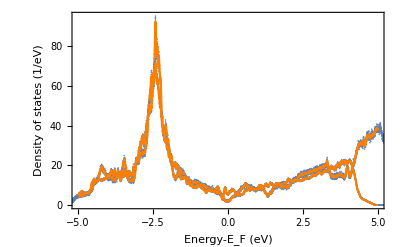

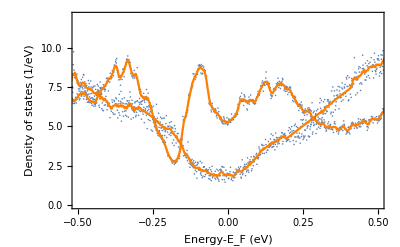

```mathematica
optionsDOSreal={FrameLabel->{Style["Energy-E_F (eV)",18],Style["Density of states (1/eV)",18]},PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True};
Show[ListPlot[pData,PlotRange->{{-B,B},All},Evaluate@optionsDOSreal],pp2,ListPlot@fData,pf2,ImageSize->400]
Show[ListPlot[pData,PlotRange->{{-B/10,B/10},{0,12}},Evaluate@optionsDOSreal],pp2,ListPlot@fData,pf2,ImageSize->400]
```

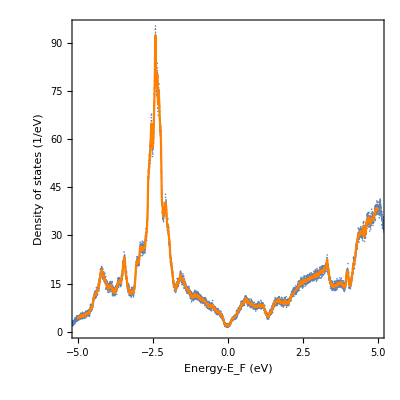

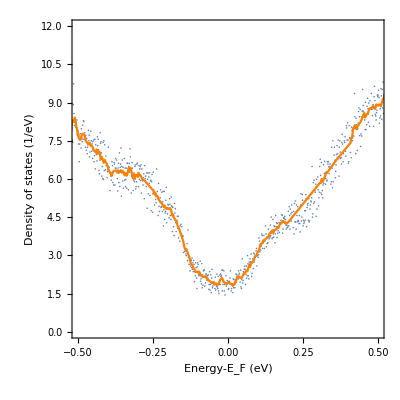

```mathematica
optionsDOSreal={AspectRatio->1,FrameLabel->{Style["Energy-E_F (eV)",18],Style["Density of states (1/eV)",18]},PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True};
Show[ListPlot[pData,PlotRange->{{-B,B},All},Evaluate@optionsDOSreal],pp2,ImageSize->400]
Show[ListPlot[pData,PlotRange->{{-B/10,B/10},{0,12}},Evaluate@optionsDOSreal],pp2,ImageSize->400]
```

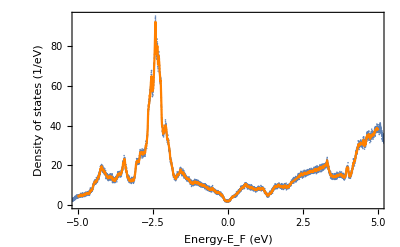

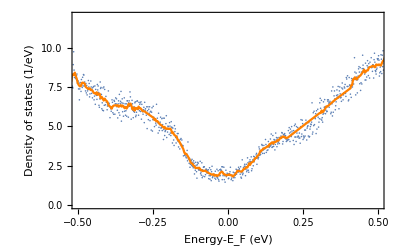

```mathematica
optionsDOSreal={FrameLabel->{Style["Energy-E_F (eV)",18],Style["Density of states (1/eV)",18]},PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True};
Show[ListPlot[pData,PlotRange->{{-B,B},All},Evaluate@optionsDOSreal],pp2,ImageSize->400]
Show[ListPlot[pData,PlotRange->{{-B/10,B/10},{0,12}},Evaluate@optionsDOSreal],pp2,ImageSize->400]
```

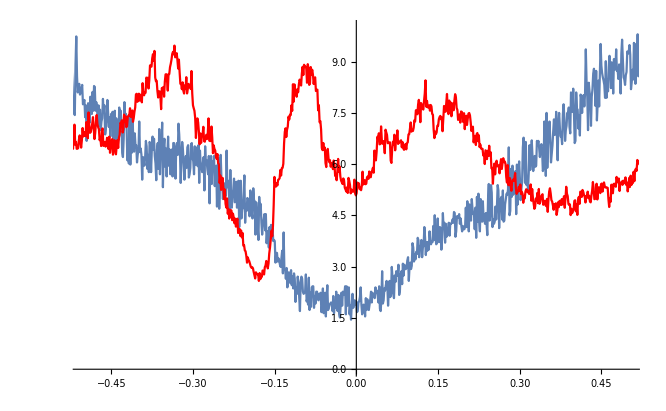

```mathematica
Show[ListLinePlot[perfDOS,PlotRange->{{-0.5,0.5},{0,10}}],ListLinePlot[frenDOS,PlotStyle->Red]]
```

```mathematica
sigmaTrealp=Table[NIntegrate[{Evaluate[pInters[energy]*sigmaK[energy,T]]},{energy,-B,B},MaxRecursion->50,PrecisionGoal->20],{T,100,4000,100}];
kappaTrealp=Table[NIntegrate[{Evaluate[pInters[energy]*kappaK[energy,T]]},{energy,-B,B},MaxRecursion->50,PrecisionGoal->20],{T,100,4000,100}];
sigmaTrealf=Table[NIntegrate[{Evaluate[fInters[energy]*sigmaK[energy,T]]},{energy,-B,B},MaxRecursion->50,PrecisionGoal->20],{T,100,4000,100}];
kappaTrealf=Table[NIntegrate[{Evaluate[fInters[energy]*kappaK[energy,T]]},{energy,-B,B},MaxRecursion->50,PrecisionGoal->20],{T,100,4000,100}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.92944 and 3.34554×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.99097 and 1.38248×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.0874 and 3.26122×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.89007×10^-6 and 8.7594×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000109389 and 1.27532×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000192549 and 5.55154×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.41766 and 7.91634×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.70941 and 6.03766×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.99322 and 4.8156×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000014142 and 3.28778×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000318947 and 1.76115×10^-21 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000499302 and 1.38543×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Flatten[sigmaTreal]
Flatten[temmps]
Table[Flatten[temmps][[i]]*Flatten[sigmaTreal][[i]],{i,1,temmps//Length}][[1]]
```

{1.92866,1.9926,2.08928,2.21843,2.37038,2.53488,2.70511,2.87736,3.04752,3.16924,3.38396,3.54756,3.70679,3.86171,4.01197,4.15815,4.30021,4.43603,4.56726,4.66722,4.81765,4.9332,5.04765,5.2005,5.26582,5.36988,5.4741,5.5727,5.6682,5.76219,5.85422,5.94462,6.03415,6.12192,6.2094,6.29483,6.37947,6.46411,6.55352,6.6381}

{100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900,4000}'

{192.866,385.732,578.598,771.464,964.33,1157.2,1350.06,1542.93,1735.79,1928.66,2121.53,2314.39,2507.26,2700.12,2892.99,3085.86,3278.72,3471.59,3664.45,3857.32,4050.19,4243.05,4435.92,4628.79,4821.65,5014.52,5207.38,5400.25,5593.12,5785.98,5978.85,6171.71,6364.58,6557.45,6750.31,6943.18,7136.04,7328.91,7521.78,7714.64}

```mathematica
Transpose[{{a,b,c},{1,2,3}}]
```

{{a,1},{b,2},{c,3}}

```mathematica
Transpose[{temmps[[1]],Flatten[kappaTreal]/Table[Flatten[temmps][[i]]*Flatten[sigmaTreal][[i]],{i,1,temmps//Length}][[1]]}]
```

{{100,2.53764×10^-8},{200,2.83666×10^-8},{300,3.3259×10^-8},{400,3.90598×10^-8},{500,4.45759×10^-8},{600,5.00296×10^-8},{700,5.51952×10^-8},{800,6.00826×10^-8},{900,6.46733×10^-8},{1000,6.89999×10^-8},{1100,7.30475×10^-8},{1200,7.67983×10^-8},{1300,8.02503×10^-8},{1400,8.33768×10^-8},{1500,8.6285×10^-8},{1600,8.90256×10^-8},{1700,9.15039×10^-8},{1800,9.38982×10^-8},{1900,9.60651×10^-8},{2000,9.80701×10^-8},{2100,1.00018×10^-7},{2200,1.01893×10^-7},{2300,1.03763×10^-7},{2400,1.056×10^-7},{2500,1.0745×10^-7},{2600,1.09354×10^-7},{2700,1.1146×10^-7},{2800,1.13489×10^-7},{2900,1.15593×10^-7},{3000,1.17606×10^-7},{3100,1.19867×10^-7},{3200,1.22174×10^-7},{3300,1.24598×10^-7},{3400,1.27102×10^-7},{3500,1.29577×10^-7},{3600,1.32232×10^-7},{3700,1.34964×10^-7},{3800,1.37748×10^-7},{3900,1.40593×10^-7},{4000,1.43476×10^-7}}

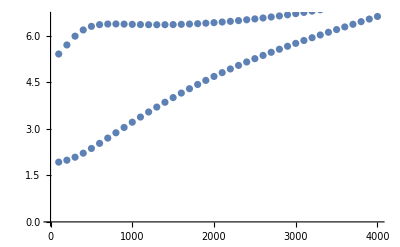

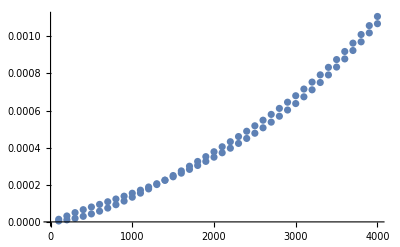

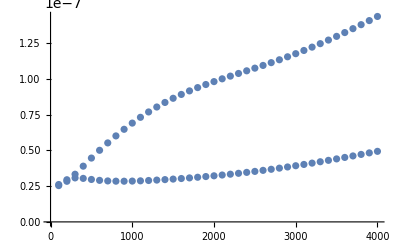

```mathematica
Show[ListPlot[Transpose[{temmps[[1]],Flatten@sigmaTrealp}]],ListPlot[Transpose[{temmps[[1]],Flatten@sigmaTrealf}]]]
Show[ListPlot[Transpose[{temmps[[1]],Flatten@kappaTrealp}]],ListPlot[Transpose[{temmps[[1]],Flatten@kappaTrealf}]]]
Show[ListPlot[Transpose[{temmps[[1]],Flatten[kappaTrealp]/Table[Flatten[temmps][[i]]*Flatten[sigmaTreal][[i]],{i,1,temmps//Length}][[1]]}]],ListPlot[Transpose[{temmps[[1]],Flatten[kappaTrealf]/Table[Flatten[temmps][[i]]*Flatten[sigmaTrealf][[i]],{i,1,temmps//Length}][[1]]}]]]
```

```mathematica
t=10^-8;
```

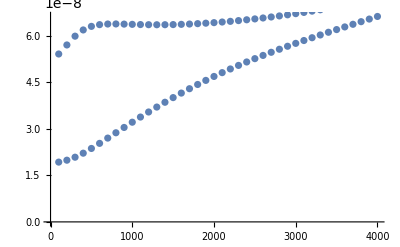

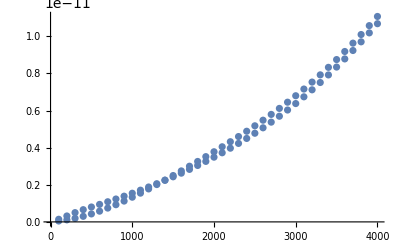

-Graphics-

```mathematica
Show[ListPlot[Transpose[{temmps[[1]],t*Flatten@sigmaTrealp}]],ListPlot[Transpose[{temmps[[1]],t*Flatten@sigmaTrealf}]]]
Show[ListPlot[Transpose[{temmps[[1]],t*Flatten@kappaTrealp}]],ListPlot[Transpose[{temmps[[1]],t*Flatten@kappaTrealf}]]]
Show[ListPlot[Transpose[{temmps[[1]],Flatten[kappaTrealp]/Table[Flatten[temmps][[i]]*Flatten[sigmaTreal][[i]],{i,1,temmps//Length}][[1]]}]],ListPlot[Transpose[{temmps[[1]],Flatten[kappaTrealf]/Table[Flatten[temmps][[i]]*Flatten[sigmaTrealf][[i]],{i,1,temmps//Length}][[1]]}]]]
```

```mathematica
plotopts={PlotLegends->Placed[SwatchLegend[{"300K","800K","1300K","1800K","2300K","2800K","3200K","3700K"}],{0.90,0.5}],AxesOrigin->{-3.5,0},Frame->True,FrameTicks->{{None,None},{Automatic,Automatic}},FrameLabel->{{"",""},{"E-E_F (eV)",""}}}
```

{PlotLegends→Placed[SwatchLegend[{300K,800K,1300K,1800K,2300K,2800K,3200K,3700K}],{0.9,0.5}],AxesOrigin→{-3.5,0},Frame→True,FrameTicks→{{None,None},{Automatic,Automatic}},FrameLabel→{{,},{E-E_F (eV),}}}

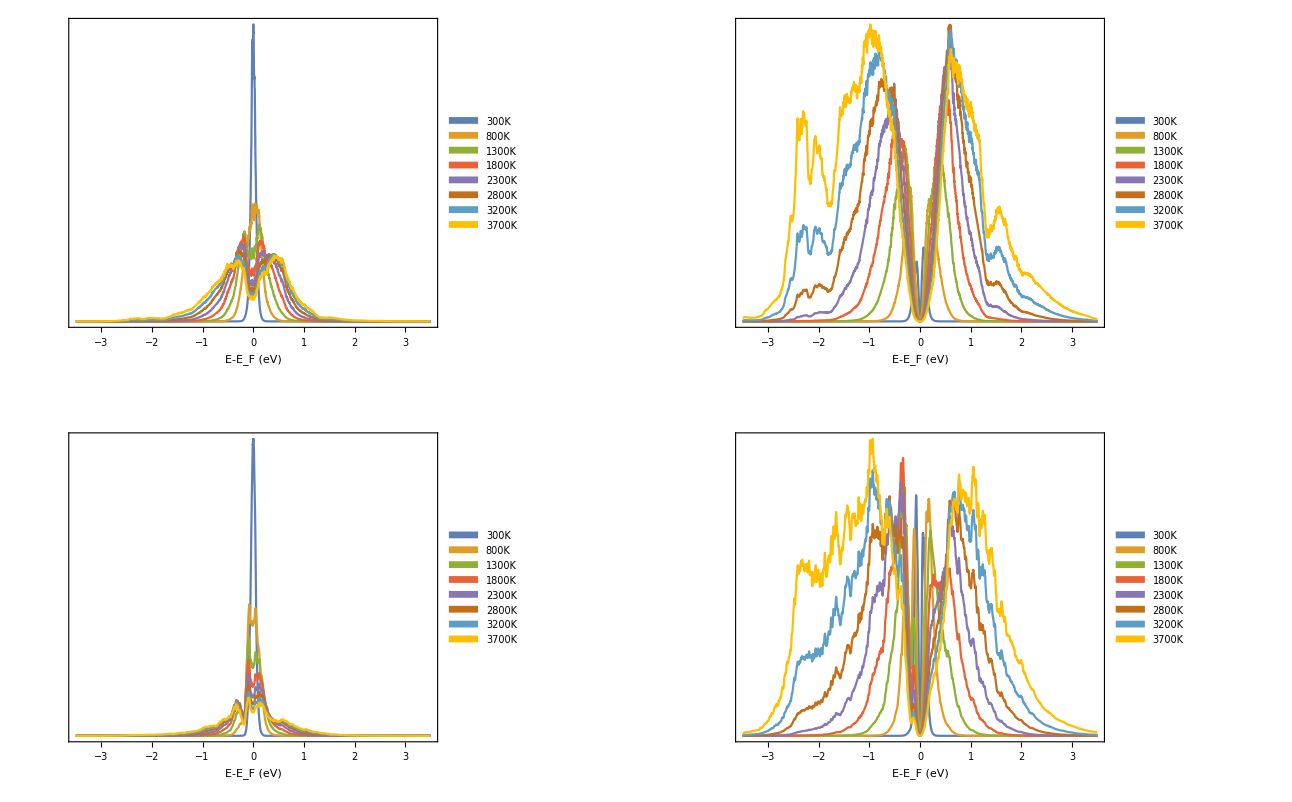

```mathematica
GraphicsGrid[{{Plot[Evaluate[Table[pInters[energy]*sigmaK[energy,T],{T,300,3800,500}]],{energy,-3.5,3.5},PlotRange->All,ImageSize->600,Evaluate@plotopts],Plot[Evaluate[Table[pInters[energy]*kappaK[energy,T],{T,300,3800,500}]],{energy,-3.5,3.5},PlotRange->All,ImageSize->600,Evaluate@plotopts]},{Plot[Evaluate[Table[fInters[energy]*sigmaK[energy,T],{T,300,3800,500}]],{energy,-3.5,3.5},PlotRange->All,ImageSize->600,Evaluate@plotopts],Plot[Evaluate[Table[fInters[energy]*kappaK[energy,T],{T,300,3800,500}]],{energy,-3.5,3.5},PlotRange->All,ImageSize->600,Evaluate@plotopts]}}]
```

```mathematica
Table[NIntegrate[Evaluate[pInters[energy]*sigmaK[energy,T]],{energy,-B,B}],{T,100,200,100}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.000155416}. NIntegrate obtained 1.92866 and 0.00474373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.000155416}. NIntegrate obtained 1.9926 and 0.00692669 for the integral and error estimates.

{1.92866,1.9926}

```mathematica
Table[NIntegrate[Evaluate[(pInterh[x]/.x->energy)*sigmaK[energy,T]],{energy,-0.4,0.4}],{T,100,200,100}]
```

{1.92813,1.99005}

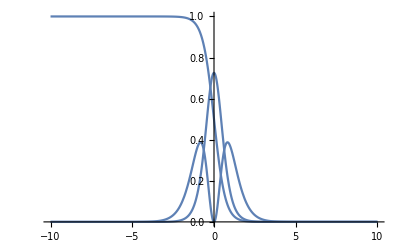

```mathematica
Show[Plot[Evaluate@{sigmaK[energy,4000]/NIntegrate[sigmaK[energy,4000],{energy,-2B,2B}]},{energy,-2B,2B},PlotRange->All],Plot[Evaluate@{kappaK[energy,4000]/NIntegrate[kappaK[energy,4000],{energy,-2B,2B}]},{energy,-2B,2B},PlotRange->All],Plot[Evaluate@{fermiDirac[energy,4000]},{energy,-2B,2B},PlotRange->All]]
```

```mathematica
Table[i/(K2eV*4000),{i,1,40}]
```

{2.90113,5.80226,8.70339,11.6045,14.5056,17.4068,20.3079,23.209,26.1102,29.0113,31.9124,34.8136,37.7147,40.6158,43.5169,46.4181,49.3192,52.2203,55.1215,58.0226,60.9237,63.8249,66.726,69.6271,72.5282,75.4294,78.3305,81.2316,84.1328,87.0339,89.935,92.8362,95.7373,98.6384,101.54,104.441,107.342,110.243,113.144,116.045}

```mathematica
K2eV*4000
```

0.344693

```mathematica
Tmelt=3800
B=5
Bkb=B/(K2eV*Tmelt)
Ival=0.05
```

3800

5

15.2691

0.05

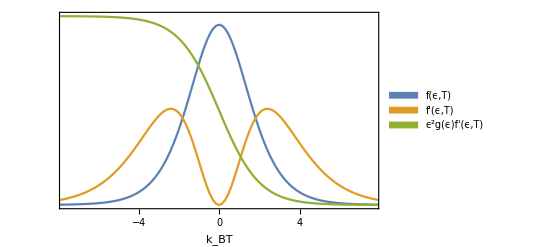

```mathematica
ListLinePlot[{Transpose[{Table[energy/(K2eV*Tmelt),{energy,-B,B,Ival}],Table[Evaluate[sigmaK[energy,Tmelt]/NIntegrate[sigmaK[energy,Tmelt],{energy,-B,B}]],{energy,-B,B,Ival}]}],Transpose[{Table[energy/(K2eV*Tmelt),{energy,-B,B,Ival}],Table[Evaluate[kappaK[energy,Tmelt]/NIntegrate[kappaK[energy,Tmelt],{energy,-B,B}]],{energy,-B,B,Ival}]}],Transpose[{Table[energy/(K2eV*Tmelt),{energy,-B,B,Ival}],Table[Evaluate[fermiDirac[energy,Tmelt]/NIntegrate[fermiDirac[energy,Tmelt],{energy,-B/4,B/4}]],{energy,-B,B,Ival}]}]},PlotRange->{{-Bkb*0.5,Bkb*0.5},All},PlotLegends->Placed[SwatchLegend[{"f(ϵ,T)","f'(ϵ,T)","ϵ^2g(ϵ)f'(ϵ,T)"}],{0.85,0.75}],AxesOrigin->{-Bkb*0.66,0},Frame->True,FrameTicks->{{None,None},{Automatic,None}},FrameLabel->{{"",""},{"k_BT",""}}]
```

```mathematica
w
```

## Lorenz real

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_Mermin_QHA_PERF_KP191919"];
filesLorenz={"T_lorenz_Perf"};
lorenz=Table[ReadList[filesLorenz[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,1}];
```

{PlotRange→{{200,3800},{1/50000000,5.5×10^-8}},AspectRatio→1,FrameLabel→{T,Lorenz number},PlotStyle→Thickness[0.01],FrameTicksStyle→15,Frame→True,ImageSize→400}

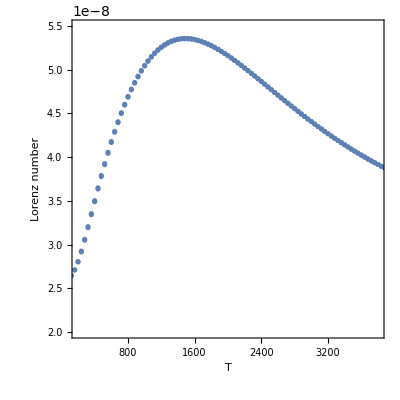

```mathematica
optionsRealLorenz={PlotRange->{{200,3800},{2*10^-8,5.5*10^-8}},AspectRatio->1,FrameLabel->{Style["T",15],Style["Lorenz number",15]},PlotStyle->Thickness[0.01],FrameTicksStyle->15,Frame->True,ImageSize->400}

ListPlot[Transpose@{Transpose[lorenz[[1]]][[1]],Transpose[lorenz[[1]]][[8]]},Evaluate@optionsRealLorenz]
```

{PlotRange→{{200,3800},{1/50000000,7.5×10^-8}},FrameLabel→{T,Lorenz number},PlotStyle→Thickness[0.01],FrameTicksStyle→15,Frame→True,ImageSize→350}

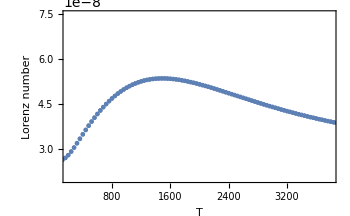

```mathematica
optionsRealLorenz2={PlotRange->{{200,3800},{2*10^-8,7.5*10^-8}},FrameLabel->{Style["T",15],Style["Lorenz number",15]},PlotStyle->Thickness[0.01],FrameTicksStyle->15,Frame->True,ImageSize->350}

ListPlot[Transpose@{Transpose[lorenz[[1]]][[1]],Transpose[lorenz[[1]]][[8]]},Evaluate@optionsRealLorenz2]
```